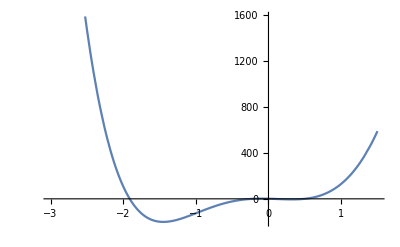

{{xx→-1.9101},{xx→-0.214731},{xx→0.0527088},{xx→0.494985},{xx→8.78857-4.02618 ⅈ},{xx→8.78857+4.02618 ⅈ}}

```mathematica
eps=0.5*10^-5;
δ=0.01;
f[x_]:=x^6-16 x^5+65 x^4+160 x^3-65 x^2-16x+1;
fx[x_]:=6 x^5-80 x^4+260 x^3+480 x^2-130x-16;
fxx[x_]:=30 x^4-320 x^3+780 x^2+960x-130;

Plot[f[x],{x,-3,1.5}]
Solve[f[xx]==0,xx]//N
x0list={-1.95, -0.25, 0.1, 0.47};
multiplicities={1,1,1,1};
n=4;

nextx[currentx_]:=currentx-f[currentx]/fx[currentx];
(* nextxWithMultiplicity[currentx_,k_]:=currentx-k f[currentx]/fx[currentx]; *)
```

```mathematica
For[i=0,i<n,i++,
	x0=x0list[[i+1]]; (*Subscript[x, n]=Subscript[x, 0] в этом моменте*)
	
	B=Abs[1/fx[x0]];
	η=Abs[f[x0]/fx[x0]];
	K=First[FindMaximum[{Abs[fxx[x]],Abs[x-x0]≤δ},{x,x0}]];
	Print["h = ",B*η*K];
	
	Subscript[x, n]=x0;
	Subscript[x, n+1]=nextx[Subscript[x, n]];
	iterations=0;
	
	While[Abs[Subscript[x, n+1]-Subscript[x, n]]>eps,
		{Subscript[x, n],Subscript[x, n+1]}={Subscript[x, n+1],nextx[Subscript[x, n+1]]};
		iterations++;
	];
	Print[i+1," корень = ",Subscript[x, n+1]//N,", ", iterations, " итераций, f(x) = ", f[Subscript[x, n+1]]//N];
];
```

h = 0.120617

1 корень = -1.9101, 3 итераций, f(x) = 1.13687×10^-13

h = 0.233992

2 корень = -0.214731, 3 итераций, f(x) = -2.80442×10^-13

h = 0.070883

3 корень = 0.0527088, 3 итераций, f(x) = 1.70003×10^-16

h = 0.254281

4 корень = 0.494985, 3 итераций, f(x) = 7.10543×10^-15